```mathematica
Quiet@Remove["`*"]
```

## Constants

```mathematica
angle=(-3π)/4;
```

```mathematica
Δangle=π/4;
```

```mathematica
Δangle=π/40
```

π/40

```mathematica
lower=angle-Δangle;
```

```mathematica
upper=angle+Δangle;
```

## Graphical Elements

```mathematica
r=0.01
```

0.01

```mathematica
circle=circleArc=Graphics[{Thickness[r],Circle[{0,0},1,{0,2Pi}]}];
```

```mathematica
circleArc=Graphics[{Thickness[r],RGBColor[255/255,204/255,20/255],Circle[{0,0},1,{lower,upper}]}];
```

```mathematica
arrowAngle=Graphics[{Thickness[r],Arrow[{{0,0},{Cos[angle],Sin[angle]}}]}];
```

```mathematica
arrowLower=Graphics[{Thickness[r],RGBColor[255/255,204/255,20/255],{Dashed,Arrow[{{0,0},{Cos[lower],Sin[lower]}}]}}];
```

```mathematica
arrowUpper=Graphics[{Thickness[r],,RGBColor[255/255,204/255,20/255],{Dashed,Arrow[{{0,0},{Cos[upper],Sin[upper]}}]}}];
```

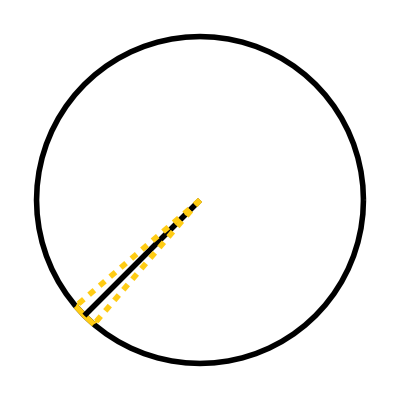

```mathematica
Show[circle,circleArc,arrowAngle,arrowLower,arrowUpper]
```